```mathematica
data=Import["/Users/samiyrjanheikki/Downloads/HEPData-ins617784-v1-csv/Table1.csv"];
pT=data[[All,1]];
σ=data[[All,4]];
```

```mathematica
data2=Import["/Users/samiyrjanheikki/Documents/FYS/FYSS9470 Erikoistyö/Pythia/data.csv"];
pT2=data2[[All,1]];
σ2=data2[[All,2]];
```

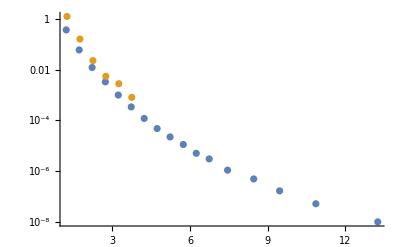

```mathematica
Show[ListLogPlot[Transpose[{pT,σ}]],ListLogPlot[Transpose[{pT2,σ2}],PlotStyle->ColorData[97,"ColorList"][[2]]],PlotRange->All]
```